```mathematica
Quit
```

```mathematica
(* Definitions *)
```

```mathematica
(* Set the directory *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb];
```

```mathematica
(* Various scales and data *)
```

```mathematica
(* Various params *)
Tcmb=2.7255;
c=299792.458;
cH0=2997.92458;
KtoeV=8.621738*10^-5;
cmtoeV=1/8065.544005;
ρcr=8.098*10^-11 h^2 eV^4;
```

```mathematica
(* DE equation of state w(a) and energy density f(a) *)
w[a_,w0_,wa_,n_]:=w0+wa (1-a)^n
f[a_,w0_,wa_,n_]:=a^(-3 (1+w0+wa)) ⅇ^(-3 wa HarmonicNumber[n]+3 a n wa HypergeometricPFQ[{1,1,1-n},{2,2},a])
(*
 Tests: 
-1-1/3 a D[Log[f[a,w0,wa]],a]-w[a,w0,wa]//Simplify
Exp[-3Integrate[(1+w[aa,w0,wa])/aa,{aa,1,a},GenerateConditions->False]]//PowerExpand//FullSimplify
 *)
```

```mathematica
(* E=H/H0 for the CPL model *) 
Ωγh2=Pi^2/30 gγ T^4/ρcr h^2/.T->Tcmb K/.gγ->2/.GeV->10^9 eV/.K->KtoeV eV//FullSimplify;
Ωγ[h_]:=Ωγh2/h^2;
Ων[h_,Neff_]:=Neff*7/8(4/11)^(4/3)Ωγ[h]
aeq[om_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=(Ωγ[h]+Ων[h,Neff])/om;
HΛ[a_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h,Neff]/a)+a^-2 ok+(1-om(1+aeq[om,h,Neff])-ok)f[a,w0,wa,n]]
```

```mathematica
(* E=H/H0 for the GREAT model *) 
ai=10^-11;
solgreat[Ωm_,Ωk_,h_,Neff_]:=solgreat[Ωm,Ωk,h,Neff]=NDSolve[{1/τ'[a]==a^2(Ωm a^-3(1+aeq[Ωm,h,Neff]/a)+Ωk a^-2+4 Pi/3 Ωk a^-2 Sinh[2τ[a]])^(1/2),τ[ai]==ai/(√(Ωγ[h]+Ων[h,Neff]))},τ[a],{a,ai,1.5},MaxSteps->10^6]
H[A_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=100h Sqrt[om a^-3(1+aeq[om,h,Neff]/a)+ok a^-2+4 Pi/3 ok a^-2 Sinh[2τ[a]]]/.solgreat[om,ok,h,Neff][[1]]/.a->A
(* Sound speed *) 
cs[a_?NumberQ,obh2_?NumberQ]:=c/Sqrt[3(1+3/4 obh2/Ωγh2 a)];
(* Redshift at decoupling (see Eqs. (66)-(68) in Komatsu et al.2009) *)
zcmbHE[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(om h^2)^(0.560/(1+21.1(obh2)^1.81)))
(* Drag redshift (see Eq. (4) of Hu astro-ph/9709112) *)
zdragHE[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1291 ((om h^2)^0.251)/(1+0.659 (om h^2)^0.828)(1+(0.313(om h^2)^-0.419(1+0.607(om h^2)^0.674))(obh2)^(0.238(om h^2)^0.223))
(* Same expressions but improved with GA, see 2106.00428 *)
zcmbGA[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=(391.672 (om h^2)^-0.372296+937.422 obh2^-0.97966)/((om h^2)^-0.0192951 obh2^-0.93681)+(om h^2)^-0.731631;
zdragGA[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=(1+428.169 obh2^0.256459 (om h^2)^0.616388+925.56 (om h^2)^0.751615)/(om h^2)^0.714129;
(* Final expressions // We use the GA fits :D  *)
zcmb[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=zcmbGA[om,obh2,h]
zdrag[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=zdragGA[om,obh2,h]
```

```mathematica
(* Proper (not comoving) angular diameter distance with curvature, see Komatsu et al. 0803.0547 Eq. (2) zcmb[om,obh2] *)
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,0,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=(DLsol[om,0,w0,wa,n,h,Neff]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,0,w0,wa,n,h,Neff]/(100h)),dL[0]==0},dL,{zz,0,2000},MaxSteps->Infinity])
DLsol[om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=(DLsol[om,ok,w0,wa,n,h,Neff]=NDSolve[{D[1/(√ok)ArcSinh[dL[zz]/(1+zz)√ok],zz]==1/(H[1/(1+zz),om,ok,w0,wa,n,h,Neff]/(100h)),dL[0]==0},dL,{zz,0,2000},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,0,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=(c/(100h)dL[z]/.DLsol[om,0,w0,wa,n,h,Neff])[[1]]//Chop
DL[z_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=(c/(100h)dL[z]/.DLsol[om,ok,w0,wa,n,h,Neff])[[1]]//Chop
(* Equation (1.5.44) from Weinberg, Cosmology pg 42 *)
dLWeinberg[z_,om_,0,w0_,wa_,n_,h_,Neff_]:=c/(100h)(1+z)NIntegrate[1/H[1/(1+zz),om,0,w0,wa,n,h,Neff]/(100h),{zz,0,z}]
dLWeinberg[z_,om_,ok_,w0_,wa_,n_,h_,Neff_]:=c/(100h)(1+z)1/(√ok)Sinh[√ok NIntegrate[1/H[1/(1+zz),om,ok,w0,wa,n,h,Neff]/(100h),{zz,0,z}]]
```

```mathematica
(* Angular diameter distance with curvature, see Komatsu et al. 0803.0547  *)
(* Tested with http://www.astro.ucla.edu/~wright/CosmoCalc.html *)
DA[z_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=1/(1+z)^2 DL[z,om,ok,w0,wa,n,h,Neff]
(* Comoving sound horizon at drag redshift *)
rs[ze_,om_?NumberQ,obh2_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=NIntegrate[cs[x,obh2]/(x^2 H[x,om,ok,w0,wa,n,h,Neff]),{x,10^-11,1/(1+ze[om,obh2,h])}]
(* Dilation scale *)
Dv[zbao_,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_]:=((DL[zbao,om,ok,w0,wa,n,h,Neff]/(1+zbao))^2  (c*zbao)/H[1/(1+zbao),om,ok,w0,wa,n,h,Neff])^(1/3)
(* BAO Subscript[d, z] ratio *)
dz[zbao_,om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=rs[zdrag,om,obh2,ok,w0,wa,n,h,Neff]/Dv[zbao,om,ok,w0,wa,n,h,Neff]
(* DH "distance" *)
DH[z_?NumberQ,om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=c/H[1/(1+z),om,ok,w0,wa,n,h,Neff]
(* DM "distance" ratio over rs(zd) *)
DM[z_?NumberQ,om_?NumberQ,obh2_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=((1+z)DA[z,om,ok,w0,wa,n,h,Neff])/rs[zdrag,om,obh2,ok,w0,wa,n,h,Neff]
(* Scaled distance at recombination *)
R[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=√(om (100h)^2)DA[zcmb[om,obh2,h],om,ok,w0,wa,n,h,Neff](1+zcmb[om,obh2,h])/c
(* Angular scale of sound horizon at recombination *)
la[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=π (DA[zcmb[om,obh2,h],om,ok,w0,wa,n,h,Neff](1+zcmb[om,obh2,h]))/(rs[zcmb,om,obh2,ok,w0,wa,n,h,Neff])
```

```mathematica
(* CMB: Planck18 with Ωk free *)
```

```mathematica
(* Central values and 1-σ errors for {R, Subscript[l, a], Subscript[Ω, b] h^2, h} from Planck 2018 for non-flat universe "base omegak plikHM TTTEEE lowl lowE lensing" likelihood *)
datacmb={1.7444755702930836,302.2179240583841,0.02248723560215764,0.635493699949593};
σCMB={0.005106275358526147,0.09128866770316652,0.0001606688957700398,0.02231669343650414};
(* Inverse Covariance Matrix using  for {R, Subscript[l, a], Subscript[Ω, b] h^2, h} *)
CijCMB=10^-8{{2604.4438327981247,16594.364939008068,-58.52126185624546,4633.200887434471},{16594.364939008068,738151.9231591133,-410.2631333284682,20120.28532331046},{-58.52126185624546,-410.2631333284682,2.5814494067963927,-93.88730018062311},{4633.200887434471,20120.28532331046,-93.88730018062311,49803.480593890716}};
invcov=Inverse[CijCMB];
(* χ^2 for R *)
vec[om_?NumberQ,obh2_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:={R[om,obh2,ok,w0,wa,n,h,Neff]-datacmb[[1]],la[om,obh2,ok,w0,wa,n,h,Neff]-datacmb[[2]],obh2-datacmb[[3]],h-datacmb[[4]]};
chi2R[om_?NumberQ,obh2_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=vec[om,obh2,ok,w0,wa,n,h,Neff].invcov.vec[om,obh2,ok,w0,wa,n,h,Neff]
```

```mathematica
(* BAO: 6dFGS + WiggleZ + eBOSS + DES yr3 *)
```

```mathematica
(* ΛCDM *)
```

```mathematica
(* 6dFGs and WiggleZ BAO data, see 1605.02702 *)
databao={{0.106,0.336,0.015},{0.44,0.073,0.031},{0.6,0.0726,0.0164},{0.73,0.0592,0.0185}};
Cijbaoinv=({{1/databao[[1,3]]^2, 0, 0, 0}, {0, 1040.3, -807.5, 336.8}, {0, -807.5, 3720.3, -1551.9}, {0, 336.8, -1551.9, 2914.9}});
vecbaoΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=Table[(databao[[i,2]]-dz[databao[[i,1]],om,obh2,ok,w0,wa,n,h,Neff]),{i,1,Length[databao]}];
chi2bao6dFWigΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=vecbaoΛ[om,obh2,ok,w0,wa,n,h,Neff].Cijbaoinv.vecbaoΛ[om,obh2,ok,w0,wa,n,h,Neff]
```

```mathematica
(* BAO measurement for MGS and eBOSS ELG is DV/rs=1/dz! (2007.08991) *)
dataMGSELG={{0.15,4.465666824,0.1681350461},{0.85,18.33,(0.57+0.62)/2}};
chi2MGSELGΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=Sum[((dataMGSELG[[i,2]]-1/dz[dataMGSELG[[i,1]],om,obh2,ok,w0,wa,n,h,Neff])/dataMGSELG[[i,3]])^2,{i,1,Length[dataMGSELG]}]
```

```mathematica
(* BAO measurements from DES 3yr (2107.04646) is DM=(1+z)*Da/rs! *)
dataDES3={0.835,18.92,0.51};
chi2DESΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=(1/dataDES3[[3]](dataDES3[[2]]-DM[dataDES3[[1]],om,obh2,ok,w0,wa,n,h,Neff]))^2;
```

```mathematica
(* BAO measurements eBOSS - LRG (2007.08991) *)
dataLRG=Import[".\\data\\sdss_DR16_LRG_v12_bao.txt","Table"];
dataLRGCijinv=Inverse[Import[".\\data\\sdss_DR16_LRG_v12_bao_covtot.txt","Table"]];
vecLRGΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:={dataLRG[[1,2]]-DM[dataLRG[[1,1]],om,obh2,ok,w0,wa,n,h,Neff],dataLRG[[2,2]]-DH[dataLRG[[2,1]],om,ok,w0,wa,n,h,Neff]/rs[zdrag,om,obh2,ok,w0,wa,n,h,Neff]}
chi2LRGΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=vecLRGΛ[om,obh2,ok,w0,wa,n,h,Neff].dataLRGCijinv.vecLRGΛ[om,obh2,ok,w0,wa,n,h,Neff]
```

```mathematica
(* BAO measurements eBOSS - Quasars (2007.08991) *)
dataQSO=Import[".\\data\\sdss_DR16_QSO_BAO_DMDH.txt","Table"];
dataQSOCijinv=Inverse[Import[".\\data\\sdss_DR16_QSO_BAO_DMDH_covtot.txt","Table"]];
vecQSOΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:={dataQSO[[1,2]]-DM[dataQSO[[1,1]],om,obh2,ok,w0,wa,n,h,Neff],dataQSO[[2,2]]-DH[dataQSO[[2,1]],om,ok,w0,wa,n,h,Neff]/rs[zdrag,om,obh2,ok,w0,wa,n,h,Neff]}
chi2QSOΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=vecQSOΛ[om,obh2,ok,w0,wa,n,h,Neff].dataQSOCijinv.vecQSOΛ[om,obh2,ok,w0,wa,n,h,Neff]
```

```mathematica
(* BAO measurements from Lya are {DH/rs,DM/rs}! *)
(* Joint Lya auto+cross correlation (with QSOs) measurement from 2007.08995, see Eq. (43) *)
dataLya={{2.334,8.99,√(0.2^2+0.38^2)},{2.334,37.5,√(1.2^2+2.5^2)}};
ρLya=-0.45;
CijLyainv=Inverse[{{dataLya[[1,3]]^2,ρLya dataLya[[1,3]] dataLya[[2,3]]},{ρLya dataLya[[1,3]] dataLya[[2,3]],dataLya[[2,3]]^2}}];
vecLyaΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:={dataLya[[1,2]]-DH[dataLya[[1,1]],om,ok,w0,wa,n,h,Neff]/rs[zdrag,om,obh2,ok,w0,wa,n,h,Neff],dataLya[[2,2]]-DM[dataLya[[2,1]],om,obh2,ok,w0,wa,n,h,Neff]};
chi2LyaΛ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=vecLyaΛ[om,obh2,ok,w0,wa,n,h,Neff].CijLyainv.vecLyaΛ[om,obh2,ok,w0,wa,n,h,Neff]
```

```mathematica
(* eBOSS Galaxy samples DR12, Table 3 in 2007.08991 *)
dataDR12=Import[".\\data\\sdss_DR12_LRG_BAO_DMDH.txt","Table"];
dataDR12Cijinv=Inverse[Import[".\\data\\sdss_DR12_LRG_BAO_DMDH_covtot.txt","Table"]];
vecDR12Λ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:={dataDR12[[1,2]]-DM[dataDR12[[1,1]],om,obh2,ok,w0,wa,n,h,Neff],
dataDR12[[2,2]]-DH[dataDR12[[2,1]],om,ok,w0,wa,n,h,Neff]/rs[zdrag,om,obh2,ok,w0,wa,n,h,Neff],
dataDR12[[3,2]]-DM[dataDR12[[3,1]],om,obh2,ok,w0,wa,n,h,Neff],dataDR12[[4,2]]-DH[dataDR12[[4,1]],om,ok,w0,wa,n,h,Neff]/rs[zdrag,om,obh2,ok,w0,wa,n,h,Neff]}
chi2DR12Λ[om_,obh2_,ok_,w0_,wa_,n_,h_,Neff_]:=vecDR12Λ[om,obh2,ok,w0,wa,n,h,Neff].dataDR12Cijinv.vecDR12Λ[om,obh2,ok,w0,wa,n,h,Neff]
```

```mathematica
(* Total BAO chi^2 *)
chi2baoΛ[om_?NumberQ,obh2_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=chi2bao6dFWigΛ[om,obh2,ok,w0,wa,n,h,Neff]+chi2MGSELGΛ[om,obh2,ok,w0,wa,n,h,Neff]+chi2DESΛ[om,obh2,ok,w0,wa,n,h,Neff]+chi2LRGΛ[om,obh2,ok,w0,wa,n,h,Neff]+chi2QSOΛ[om,obh2,ok,w0,wa,n,h,Neff]+chi2LyaΛ[om,obh2,ok,w0,wa,n,h,Neff]+chi2DR12Λ[om,obh2,ok,w0,wa,n,h,Neff]
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* SnIa: Pantheon // corrected *)
```

```mathematica
(* Data *)
```

```mathematica
SnIapath=NotebookDirectory[]<>".\\data\\data_Pantheon\\";
```

```mathematica
dataPanth=Import[SnIapath<>"lcparam_full_long_zhel.txt","Table"];
ndatPanth=Length[dataPanth]-1;
filecovs="sys_full_long.zip";
zmax=dataPanth[[2;;-1,2]]//Max;
```

```mathematica
Dij0=Import[SnIapath<>filecovs,{"ZIP","sys_full_long.txt","List"}];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
Dij0=.
Id=ConstantArray[1,ndatPanth];
Cijtot=DiagonalMatrix[dataPanth[[All,6]][[2;;-1]]^2]+Dij;
InvCij=Inverse[Cijtot];
```

```mathematica
(* end *)
```

```mathematica
(* SnIa ΛCDM: Pantheon // corrected *)
```

```mathematica
chi2Panthmarge[om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=Module[{Δm,A,B,Ee},
Δm=Table[dataPanth[[1+i,5]]-(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DL[dataPanth[[1+i,2]],om,ok,w0,wa,n,h,Neff]]+25),{i,1,ndatPanth}];
A=Δm.InvCij.Δm;
B=Δm.InvCij.Id;
Ee=Id.InvCij.Id;
A+Log[Ee/(2Pi)]-B^2/Ee]
```

```mathematica
M0Panthmarge[om_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=Module[{Δm,A,B,Ee},
Δm=Table[dataPanth[[1+i,5]]-(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DL[dataPanth[[1+i,2]],om,ok,w0,wa,n,h,Neff]]+25),{i,1,ndatPanth}];
A=Δm.InvCij.Δm;
B=Δm.InvCij.Id;
Ee=Id.InvCij.Id;
B/Ee]
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* H(z) χ^2 term *)
```

```mathematica
(* Read the H(z) data *)
(* Most from Moresco(1601.01701) +some from clustering, see 1512.07703 *)
```

```mathematica
dataHz=Join[Import[".\\data\\Hz_all_Moresco_2017.dat","Table"],Import[".\\data\\Hz_clustering.txt","Table"]];
```

```mathematica
(* chi^2 *)
```

```mathematica
chi2Hz[om_,ok_,w0_,wa_,n_,h_,Neff_]:=Sum[((dataHz[[i,2]]-H[1/(1+dataHz[[i,1]]),om,ok,w0,wa,n,h,Neff])/dataHz[[i,3]])^2,{i,1,Length[dataHz]}];
```

```mathematica
(* TRGB H0 χ^2 term *)
```

```mathematica
(* chi^2 *)
```

```mathematica
(* data from 2002.01550 *)
H0TRGB=69.6;
σH0TRGB=Sqrt[0.8^2+1.7^2];
chi2H0[om_,ok_,w0_,wa_,n_,h_,Neff_]:=((H0TRGB-H[1,om,ok,w0,wa,n,h,Neff])/σH0TRGB)^2;
```

```mathematica
(* Total chi^2 *)
```

```mathematica
(* ΛCDM *)
chi2totalΛ[om_?NumberQ,obh2_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=Module[{chi20},chi20=chi2R[om,obh2,ok,w0,wa,n,h,Neff]+chi2baoΛ[om,obh2,ok,w0,wa,n,h,Neff]+chi2Panthmarge[om,ok,w0,wa,n,h,Neff]+chi2Hz[om,ok,w0,wa,n,h,Neff]+chi2H0[om,ok,w0,wa,n,h,Neff];
DownValues[DLsol]=DownValues[DLsol][[-2;;-1]];
DownValues[solgreat]=DownValues[solgreat][[-1]];
If[Arg[chi20//Chop]==0,chi20//Chop,10^500.]]
chi2totalΛvec[om_?NumberQ,obh2_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:={chi2R[om,obh2,ok,w0,wa,n,h,Neff],chi2baoΛ[om,obh2,ok,w0,wa,n,h,Neff],chi2Panthmarge[om,ok,w0,wa,n,h,Neff],chi2Hz[om,ok,w0,wa,n,h,Neff],chi2H0[om,ok,w0,wa,n,h,Neff]}
```

```mathematica
(* end *)
```

```mathematica
(* MCMC stuff *)
```

```mathematica
(* Some code borrowed from *)
"https://mathematica.stackexchange.com/questions/6877/do-i-have-to-code-each-case-of-this-grid-full-of-plots-separately";
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
plempty[{left_,right_}]:=Plot[0,{x,-1,1},Frame->True,Axes->False,PlotStyle->White,FrameStyle->{{left,right},{White,White}},FrameTicks->None];
pleint=plempty[{Automatic,Transparent}];
pleout=plempty[{Transparent,Transparent}];
(* This is the jump function // Proposes the next point *)
jumpfunc[point_,s_]:=point+RandomVariate[NormalDistribution[0,s],Length[point]]
jumpfuncmat[point_,cijtest_]:=RandomVariate[MultinormalDistribution[point,cijtest]]
(* Δχ^2 for 2 params, up to 3σ *)
dx2=Table[2 InverseGammaRegularized[Nn/2,1-Erf[xσ/(√2)]]/.Nn->2//N,{xσ,1,3}];
(* Contours+color from the MCMC // Uses ConvexHull // Advanced++ *)
Needs["ComputationalGeometry`"];
Off[CompiledFunction::cflist];
Confid2D[data_List,color_,inter_]:=Module[{cv,cv1,cv2,qq},cv=ConvexHull[data,AllPoints->True];cv1=data[[#]]&/@cv;cv2=Join[cv1,{cv1[[1]],cv1[[2]]}];qq=Show[Graphics[{color,FilledCurve[BSplineCurve[cv2,SplineDegree->2,SplineKnots->"Unclamped"]],Antialiasing->True}],Frame->True];qq]
normalize[bins_,counts_]:=counts/Max[counts]
(* Convergence diagnostics *)
Rstatistic[chain_,param_,burnin_]:=Module[{n,m,W,B,Rminus1},
m=chain//Length;
n=Table[chain[[i,burnin;;-1,1,param]]//Length,{i,1,m}]//Mean;
W=Mean[Table[Variance[chain[[j,burnin;;-1,1,param]]],{j,1,m}]];
B=n Variance[Table[Mean[chain[[j,burnin;;-1,1,param]]],{j,1,m}]];
Rminus1=√((1-1/n)+1/n B/W)-1]
(* Utils *)
time[dt1_]:=Which[dt1<60,ToString[dt1]<>" secs",60≤dt1<1000,ToString[dt1/60.]<>" mins",1000≤dt1,ToString[dt1/3600.]<>" hrs"]
```

```mathematica
(* Cache *)
```

```mathematica
fminΛ4={490.9532181,{1071.7418497406936,{om->0.3502095025693111,obh2->0.022502891343156774,ok->0.0009609162432880226,h->0.6339344151648668}}};
```

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* Tests *)
```

```mathematica
(* Various tests *)
```

```mathematica
h0=0.6476;
om0=0.3350;
obh20=0.0225;
w00=-1;
wa0=0;
n0=1;
ok0=0.0008;
Neff0=3.046;
z0=1;
a0=1/(1+z0);
```

```mathematica
w[a0,w00,wa0,n0]
H[a0,om0,ok0,w00,wa0,n0,h0,Neff0]/(100h0)
cs[a0,obh20]/c
zcmb[om0,obh20,h0]
zdrag[om0,obh20,h0]
DL[z0,om0,obh20,ok0,w00,wa0,n0,h0]/(c/(100h0))
DA[z0,om0,obh20,ok0,w00,wa0,n0,h0]/(c/(100h0))
rs[zcmb,om0,obh20,ok0,w00,wa0,n0,h0,Neff0]
Dv[z0,om0,ok0,w00,wa0,n0,h0,Neff0]
R[om0,obh20,ok0,w00,wa0,n0,h0,Neff0]
la[om0,obh20,ok0,w00,wa0,n0,h0,Neff0]
```

-1

1.84621

0.0312387

1088.53

1060.

0.437358

0.109339

144.91

3064.89

1.7455

302.665

```mathematica
(* CMB, BAO, SnIa, H(z), Subscript[H0, Riess] *)
chi2totalΛ[om0,obh20,ok0,w00,wa0,n0,h0,Neff0]
chi2totalΛvec[om0,obh20,ok0,w00,wa0,n0,h0,Neff0]
```

1103.6

{31.7084,14.9114,1034.78,21.8395,0.358547}

```mathematica
Clear[om0,obh20,ok0,w00,wa0,n0,h0,Neff0,z0,a0]
```

```mathematica
fminΛ1=FindMinimum[chi2totalΛ[om,0.0222,0,-1,0,1,0.675,3.046],{om,0.315,0.316}]//AbsoluteTiming
```

{5.63714,{6883.78,{om→0.476404}}}

```mathematica
fminΛ2=FindMinimum[chi2totalΛ[om,obh2,0,-1,0,1,0.675,3.046],{om,0.315,0.316},{obh2,0.0220,0.0221}]//AbsoluteTiming
```

{34.1535,{5436.58,{om→0.443068,obh2→0.017908}}}

```mathematica
fminΛ3=FindMinimum[chi2totalΛ[om,obh2,ok,-1,0,1,0.675,3.046],{om,0.315,0.316},{obh2,0.0220,0.0221},{ok,0.001,0.002}]//AbsoluteTiming
```

{116.817,{1076.16,{om→0.311546,obh2→0.0224126,ok→0.000592487}}}

```mathematica
fminΛ4=FindMinimum[chi2totalΛ[om,obh2,ok,-1,0,1,h,3.046],{om,0.315,0.316},{obh2,0.0220,0.0221},{ok,0.001,0.002},{h,0.67,0.671}]//AbsoluteTiming
```

FindMinimum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{490.953,{1071.74,{om→0.35021,obh2→0.0225029,ok→0.000960916,h→0.633934}}}

```mathematica
(* end *)
```

```mathematica
(* MCMC current data *)
```

```mathematica
?chi2totalΛ
```

Global`chi2totalΛ

chi2totalΛ[om_?NumberQ,obh2_?NumberQ,ok_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ,Neff_?NumberQ]:=Module[{chi20},chi20=chi2R[om,obh2,ok,w0,wa,n,h,Neff]+chi2baoΛ[om,obh2,ok,w0,wa,n,h,Neff]+chi2Panthmarge[om,ok,w0,wa,n,h,Neff]+chi2Hz[om,ok,w0,wa,n,h,Neff]+chi2H0[om,ok,w0,wa,n,h,Neff];DownValues[DLsol]=DownValues[DLsol]⟦-2;;-1⟧;DownValues[solgreat]=DownValues[solgreat]⟦-1⟧;If[Arg[Chop[chi20]]==0,Chop[chi20],10^500.]]

```mathematica
(* Choose the params to vary *)
chi2[om_,obh2_,ok_,h_]:=chi2totalΛ[om,obh2,ok,-1,0,1,h,3.046]
```

```mathematica
(* Set the initial priors for {Subscript[Ω, m],Subscript[w, 0]} *)
params={"Ω_m","Ω_bh^2","Ω_k","h"};
priors={{0.01,0.5},{0.015,0.035},{0.00001,0.1},{0.5,1}};
nparams=priors//Length;
smallchainname="smallchain_great_TRGB";
bigchainname="bigchain_great_TRGB";
```

```mathematica
(* Do a small MCMC to get a test cov. matrix *)
```

```mathematica
ϵ0=0.01;
nn=2;
inter=ListInterpolation[ParallelTable[chi2[om,obh2,ok,h],{om,fminΛ4[[2,2,1,2]](1-nn ϵ0),fminΛ4[[2,2,1,2]](1+nn ϵ0),ϵ0 fminΛ4[[2,2,1,2]]},{obh2,fminΛ4[[2,2,2,2]](1-nn ϵ0),fminΛ4[[2,2,2,2]](1+nn ϵ0),ϵ0 fminΛ4[[2,2,2,2]]},{ok,fminΛ4[[2,2,3,2]](1-nn ϵ0),fminΛ4[[2,2,3,2]](1+nn ϵ0),ϵ0 fminΛ4[[2,2,3,2]]},{h,fminΛ4[[2,2,4,2]](1-nn ϵ0),fminΛ4[[2,2,4,2]](1+nn ϵ0),ϵ0 fminΛ4[[2,2,4,2]]},DistributedContexts->Automatic],{{fminΛ4[[2,2,1,2]](1-nn ϵ0),fminΛ4[[2,2,1,2]](1+nn ϵ0)},{fminΛ4[[2,2,2,2]](1-nn ϵ0),fminΛ4[[2,2,2,2]](1+nn ϵ0)},{fminΛ4[[2,2,3,2]](1-nn ϵ0),fminΛ4[[2,2,3,2]](1+nn ϵ0)},{fminΛ4[[2,2,4,2]](1-nn ϵ0),fminΛ4[[2,2,4,2]](1+nn ϵ0)}}]//AbsoluteTiming;
```

```mathematica
Cijtest=Inverse[1/2D[inter[[2]][om,obh2,ok,h],{{om,obh2,ok,h},2}]/.fminΛ4[[2,2]]]
```

{{0.000179388,3.05113×10^-7,1.84287×10^-6,-0.000174542},{3.05113×10^-7,1.87644×10^-8,5.42305×10^-9,-3.84765×10^-7},{1.84287×10^-6,5.42305×10^-9,1.98553×10^-8,-1.85295×10^-6},{-0.000174542,-3.84765×10^-7,-1.85295×10^-6,0.000174114}}

```mathematica
Cijtest//Diagonal//Sqrt
```

{0.0133936,0.000136983,0.000140909,0.0131952}

```mathematica
Cijtest={{0.0001793875555162422,3.051131605544637*^-7,1.8428716030603172*^-6,-0.00017454180192640758},{3.051131605544632*^-7,1.876443531052102*^-8,5.423050723467609*^-9,-3.8476510203793653*^-7},{1.8428716030603183*^-6,5.4230507234676306*^-9,1.9855338591163094*^-8,-1.8529476850453331*^-6},{-0.00017454180192640767,-3.847651020379375*^-7,-1.852947685045333*^-6,0.00017411362561846498}};
```

```mathematica
fminΛ4[[2]]
```

{1071.74,{om→0.35021,obh2→0.0225029,ok→0.000960916,h→0.633934}}

```mathematica
(* Do a small MCMC to get a test cov. matrix *)
step=0;
t1=AbsoluteTime[];
totalsteps=2000;
initpoint={0.35021,0.0225029,0.000960916,0.633934};
currentpoint=initpoint;
chi2current=chi2@@currentpoint;
smallchain={};
ProgressIndicator[Dynamic[step],{0,totalsteps}]
While[step<totalsteps+1,
(
proposedpoint=jumpfuncmat[currentpoint,Cijtest];
chi2prop=chi2@@proposedpoint;
jumpprob=Exp[-(chi2prop-chi2current)/2];
If[(RandomReal[]≤Min[{1,jumpprob}])&&(And@@IntervalMemberQ[Interval@@priors,proposedpoint]),currentpoint=proposedpoint;chi2current=chi2prop;AppendTo[smallchain,{currentpoint,chi2current}];,currentpoint=currentpoint;];
);
step++]
Print["Time needed (secs): ",AbsoluteTime[]-t1]
```

Time needed (secs): 552.1533516

```mathematica
(* Save the chain in zip format to save space *)
Export[smallchainname<>".zip",{smallchainname<>".m"->smallchain}];
```

```mathematica
(* Read in the chain // for postprocessing etc *)
smallchain=Import[smallchainname<>".zip",smallchainname<>".m"];
```

```mathematica
(* Best-fit from the MCMC *)
chi2min=Min[smallchain[[All,2]]]
bf=smallchain[[Position[smallchain,chi2min][[1,1]]]][[1]]
```

1071.85

{0.350847,0.0225209,0.00096176,0.633836}

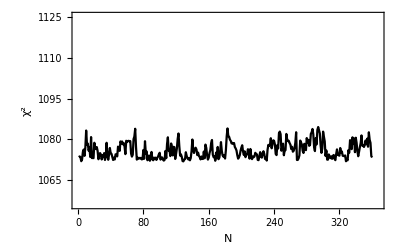

```mathematica
(* χ^2 plot *)
ListPlot[smallchain[[All,2]],Joined->True,PlotRange->{{0,1.02Length[smallchain[[All,2]]]},chi2min{0.985,1.05}},Frame->True,FrameLabel->{"N","χ^2"},PlotStyle->Black,FrameStyle->Black]
```

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[smallchain];
burnin=Round[0.1*chlen];
Cijchain0=Covariance[smallchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain0]
SymmetricMatrixQ[Cijchain0]
Cijchain0//Diagonal//Sqrt
```

{{0.000180052,-5.77792×10^-8,1.8178×10^-6,-0.000178983},{-5.77792×10^-8,1.86013×10^-8,2.01296×10^-9,-5.45533×10^-8},{1.8178×10^-6,2.01296×10^-9,1.92948×10^-8,-1.86813×10^-6},{-0.000178983,-5.45533×10^-8,-1.86813×10^-6,0.00018299}}

True

True

{0.0134183,0.000136387,0.000138906,0.0135274}

```mathematica
(* end *)
```

```mathematica
(* This is the main MCMC *)
```

```mathematica
(* Read in the chain // for postprocessing etc *)
smallchain=Import[smallchainname<>".zip",smallchainname<>".m"];
```

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[smallchain];
burnin=Round[0.1*chlen];
Cijchain0=Covariance[smallchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain0]
SymmetricMatrixQ[Cijchain0]
Cijchain0//Diagonal//Sqrt
```

{{0.000180052,-5.77792×10^-8,1.8178×10^-6,-0.000178983},{-5.77792×10^-8,1.86013×10^-8,2.01296×10^-9,-5.45533×10^-8},{1.8178×10^-6,2.01296×10^-9,1.92948×10^-8,-1.86813×10^-6},{-0.000178983,-5.45533×10^-8,-1.86813×10^-6,0.00018299}}

True

True

{0.0134183,0.000136387,0.000138906,0.0135274}

```mathematica
{Min[smallchain[[All,2]]],
smallchain[[Position[smallchain,Min[smallchain[[All,2]]]][[1,1]]]][[1]]}
```

{1071.85,{0.350847,0.0225209,0.00096176,0.633836}}

```mathematica
(* Do the MCMC *)
step=0;
t1=AbsoluteTime[];
totalsteps=300000;
initpoint={0.350847,0.0225209,0.00096176,0.633836};
currentpoint=initpoint;
chi2current=chi2@@currentpoint;
bigchain={};
ProgressIndicator[Dynamic[step],{0,totalsteps}]
While[step<totalsteps+1,
(
proposedpoint=jumpfuncmat[currentpoint,Cijchain0];
chi2prop=chi2@@proposedpoint;
jumpprob=Exp[-(chi2prop-chi2current)/2];
If[(RandomReal[]≤Min[{1,jumpprob}])&&(And@@Table[IntervalMemberQ[Interval@priors[[i]],proposedpoint[[i]]],{i,1,Length[priors]}]),currentpoint=proposedpoint;chi2current=chi2prop;AppendTo[bigchain,{currentpoint,chi2current}];,currentpoint=currentpoint;];
);
step++]
Print["Time needed (secs): ",AbsoluteTime[]-t1]
```

Time needed (secs): 84273.5677649

```mathematica
(* Save the chain in zip format to save space *)
Export[bigchainname<>".zip",{bigchainname<>".m"->bigchain}];
```

```mathematica
(* Read in the chain // for postprocessing etc *)
bigchain=Import[".//SN_chains//"<>bigchainname<>".zip",bigchainname<>".m"];
```

```mathematica
(* Best-fit from the MCMC *)
chi2min=Min[bigchain[[All,2]]]
bf=bigchain[[Position[bigchain,chi2min][[1,1]]]][[1]]
```

1071.76

{0.350269,0.0224967,0.000957623,0.634159}

```mathematica
(* Mean values from the MCMC *)
bigchain[[All,1]]//Mean
bigchain[[All,1]]//StandardDeviation
```

{0.350058,0.0224999,0.000968676,0.634646}

{0.0158824,0.000141036,0.000180467,0.014961}

```mathematica
(* χ^2 plot *)
Rasterize[ListPlot[bigchain[[All,2]],Joined->True,PlotRange->{{0,1.02Length[bigchain[[All,2]]]},chi2min{0.985,1.1}},Frame->True,FrameLabel->{"N","χ^2"},FrameStyle->Black],RasterSize->600,ImageSize->400]
```

-Graphics-

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[bigchain];
burnin=Round[0.3*chlen];
Cijchain=Covariance[bigchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain]
SymmetricMatrixQ[Cijchain]
Cijchain//Diagonal//Sqrt
```

{{0.000248061,3.08183×10^-7,2.73671×10^-6,-0.000231541},{3.08183×10^-7,1.98652×10^-8,6.09339×10^-9,-3.77581×10^-7},{2.73671×10^-6,6.09339×10^-9,3.16307×10^-8,-2.61125×10^-6},{-0.000231541,-3.77581×10^-7,-2.61125×10^-6,0.000220922}}

True

True

{0.0157499,0.000140944,0.00017785,0.0148634}

```mathematica
fminΛ4[[2]]
```

{1071.74,{om→0.35021,obh2→0.0225029,ok→0.000960916,h→0.633934}}

```mathematica
params
```

{Ω_m,Ω_bh^2,Ω_k,h}

```mathematica
MCMCchain=bigchain[[burnin;;-1]];
```

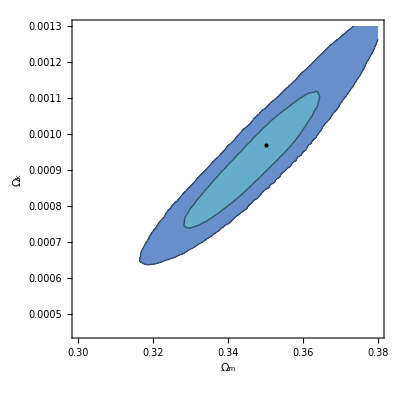

```mathematica
pp={1,3};
datapl=MCMCchain[[All,1,pp]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[nn/(√2)]/.nn->{1,2}//N];
cenp=datapl//Mean;
con1=ContourPlot[PDF[skd,{a,b}],{a, 0.3,0.38},{b, 4.5*10^-4, 13*10^-4},Contours->cons,ContourShading->{White,Hue[0.6,0.5,0.8],Hue[0.55,0.5,0.8],Hue[0.5,0.5,0.9]},FrameLabel->params[[pp]],BaseStyle->FontSize->18,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{Dashed,Black,Line[{{-2,0},{0,0}}],Line[{{-1,-4*10^-7},{-1,4*10^-7}}]},{Black,Point[cenp]},{Red,Point[{-1,0}]}},PlotRangeClipping->True]
```

```mathematica
params={"Ω_m","Ω_bh^2","Ω_k","H_0"};
```

```mathematica
LaunchKernels[7];
```

```mathematica
(*the chain*)mcmcchain=ParallelTable[{{MCMCchain[[i]][[1,1]],MCMCchain[[i]][[1,2]],MCMCchain[[i]][[1,3]],H[1,MCMCchain[[i]][[1,1]],MCMCchain[[i]][[1,3]],-1,0,1,MCMCchain[[i]][[1,4]],3.046]},MCMCchain[[i]][[2]]},{i,1,Length[MCMCchain]}];
(*The parameters of the chains as they will appear in the plot and some default (Planck) values*)
def={0.315,0.0224,0.001,67.4};
```

```mathematica
fminΛ4
fminΛ4[[2,2,All,2]]
```

{490.953,{1071.74,{om→0.35021,obh2→0.0225029,ok→0.000960916,h→0.633934}}}

{0.35021,0.0225029,0.000960916,0.633934}

```mathematica
H[1,fminΛ4[[2,2,1,2]],fminΛ4[[2,2,3,2]],-1,0,1,fminΛ4[[2,2,4,2]],3.046]
```

68.4585

```mathematica
mcmcchain[[All,1]]//Mean
mcmcchain[[All,1]]//StandardDeviation
```

{0.350084,0.0225015,0.000969007,68.4651}

{0.0157499,0.000140944,0.00017785,0.450965}

```mathematica
(* Calculate the ranges of the plots and number of ticks (default ndivs+1). Set the fontsize. *)
fontsize=12;
ndivs=3;
nmax=Length[params];
lims=Table[{Min[mcmcchain[[All,1,i]]],Max[mcmcchain[[All,1,i]]]},{i,1,nmax}];
divs=Table[FindDivisions[lims[[i]],ndivs]//N,{i,1,nmax}];
ranges=lims;
```

```mathematica
(* This makes the 1D, 2D plots and the Triangle plot *)
pl1d[i_]:=SmoothHistogram[mcmcchain[[All,1,i]],Automatic,"PDF",Frame->True,PlotRange->{ranges[[i]],All},AspectRatio->1,FrameLabel->{params[[i]],None},FrameTicks->{{None,None},{divs[[i]],Transpose[{divs[[i]],Table["",Length[divs[[i]]]]}]}},BaseStyle->FontSize->fontsize,Axes->False,FrameStyle->Black,PlotStyle->Black,Epilog->{Black,Dashed,Line[{{def[[i]],0},{def[[i]],10^5}}]}]
pl2d[i_,j_]:=Module[{datapl,skd,pdf,cons,cenp},
datapl=mcmcchain[[All,1,{i,j}]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[{1,2,3}/(√2)]//N];
cenp=datapl//Mean;
ContourPlot[PDF[skd,{a,b}],{a, ranges[[i,1]],ranges[[i,2]]},{b, ranges[[j,1]], ranges[[j,2]]},Contours->cons,ContourShading->{White,Hue[0.6,0.5,0.8],Hue[0.55,0.5,0.8],Hue[0.5,0.5,0.9]},FrameLabel->params[[{i,j}]],FrameTicks->{{divs[[j]],Transpose[{divs[[j]],Table["",Length[divs[[j]]]]}]},{divs[[i]],Transpose[{divs[[i]],Table["",Length[divs[[i]]]]}]}},BaseStyle->FontSize->fontsize,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{Black,Point[cenp]},{Red,Point[{def[[i]],def[[j]]}]}}]]
tab[i_,j_]:=Which[i==j,pl1d[i],i<j,pl2d[i,j],i==j+1,pleint,True,pleout]
```

```mathematica
(* Create the plots // most time is spent here hence parallelize *)
allplots=ParallelTable[tab[i,j],{j,1,nmax},{i,1,nmax}];
```

```mathematica
finalplot=Rasterize[Show[plotGrid[allplots,500,500,ImagePadding->60]],RasterSize->2000,ImageSize->600]
```

-Graphics-

```mathematica
Export[".//plots//cont_great_TRGB.png",finalplot]
```

.//plots//cont_great_TRGB.png

```mathematica
(* end *)
```

```mathematica
(* end *)
```

```mathematica
(* Bayes evidence // Tempered MCMC *)
```

```mathematica
(* Read in the chain // for postprocessing etc *)
bigchainname="bigchain_great_TRGB";
bigchain=Import[bigchainname<>".zip",bigchainname<>".m"];
```

```mathematica
(* Best-fit from the MCMC *)
chi2min=Min[bigchain[[All,2]]]
bf=bigchain[[Position[bigchain,chi2min][[1,1]]]][[1]]
```

1071.76

{0.350269,0.0224967,0.000957623,0.634159}

```mathematica
(* Choose the params to vary *)
chi2[om_,obh2_,ok_,h_]:=chi2totalΛ[om,obh2,ok,-1,0,1,h,3.046]
```

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[bigchain];
burnin=Round[0.01*chlen];
Cijchain=Covariance[bigchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain]
SymmetricMatrixQ[Cijchain]
Cijchain//Diagonal//Sqrt
Fijchain=Cijchain//Inverse;
```

{{0.000251528,3.22303×10^-7,2.79167×10^-6,-0.000234378},{3.22303×10^-7,1.98845×10^-8,6.25414×10^-9,-3.89239×10^-7},{2.79167×10^-6,6.25414×10^-9,3.24702×10^-8,-2.65641×10^-6},{-0.000234378,-3.89239×10^-7,-2.65641×10^-6,0.000223346}}

True

True

{0.0158596,0.000141012,0.000180195,0.0149448}

```mathematica
bfmin=fminΛ4[[2,2,All,2]]
```

{0.35021,0.0225029,0.000960916,0.633934}

```mathematica
fminΛ4[[2,1]]
```

```mathematica
errs=Cijchain//Diagonal//Sqrt
```

{0.0158596,0.000141012,0.000180195,0.0149448}

```mathematica
priors={{0.01,0.5},{0.015,0.035},{0.00001,0.1},{0.5,1}};
prior=UniformDistribution[priors];
priorpdf[{om_,obh2_,ok_,h_}]:=PDF[prior,{om,obh2,ok,h}]
```

```mathematica
likelihood=ProbabilityDistribution[Exp[-chi2[om,obh2,ok,h]/2],{om,-∞,∞},{obh2,-∞,∞},{ok,-∞,∞},{h,-∞,∞}];
```

```mathematica
posteriorpdf[{om_,obh2_,ok_,h_},λ_]:=PDF[prior,{om,obh2,ok,h}]PDF[likelihood,{om,obh2,ok,h}]^λ
posterior[λ_]:=ProbabilityDistribution[posteriorpdf[{om,obh2,ok,h},λ],{om,-∞,∞},{obh2,-∞,∞},{ok,-∞,∞},{h,-∞,∞}]
```

```mathematica
inter[data_]:=Sum[(data[[i+1,1]]-data[[i,1]]) ((data[[i,2]]+data[[i+1,2]])/2),{i,1,Length[data]-1}]
```

```mathematica
doMCMC[totalsteps_,initpoint_,priors_,Cij_,verbose_,β_]:=Module[{t1,currentpoint,PDFcurrent,smallchain,proposedpoint,PDFLprop,jumpprob,likecurrent,priorcurrent,likeprop,priorprop},
ss`step=0;
t1=AbsoluteTime[];
currentpoint=initpoint;
likecurrent=PDF[likelihood,currentpoint]^β;
priorcurrent=PDF[prior,currentpoint];
PDFcurrent=likecurrent priorcurrent;
smallchain={};
If[verbose=="ver",Print[ProgressIndicator[Dynamic[ss`step],{0,totalsteps}]]];
While[ss`step<totalsteps,
(proposedpoint=jumpfuncmat[currentpoint,Cij/β];
If[And@@IntervalMemberQ[Interval@@priors,proposedpoint],likeprop=PDF[likelihood,proposedpoint]^β;
priorprop=PDF[prior,proposedpoint];
PDFLprop=likeprop priorprop;
jumpprob=PDFLprop/PDFcurrent;
If[RandomReal[]≤Min[{1,jumpprob}],
currentpoint=proposedpoint;PDFcurrent=PDFLprop;likecurrent=likeprop;
priorcurrent=priorprop;,
currentpoint=currentpoint;],
currentpoint=currentpoint;];
AppendTo[smallchain,Log[likecurrent]/β//N];
);
ss`step++];
If[verbose=="ver",Print["Time needed (secs): ",AbsoluteTime[]-t1]];
smallchain]
```

```mathematica
LaunchKernels[7];
```

```mathematica
βsteps=20;
βs=Table[(i/βsteps)^5,{i,1,βsteps,1}];
nstep=1000;
burnin=IntegerPart[0.3 nstep];
```

```mathematica
(*doMCMC[100,bfmin,priors,1000Cijchain,"ver",1]*)
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb,NIntegrate::slwcon,NDSolve::ndsz,InterpolatingFunction::dmval,Power::infy,NDSolve::nlnum,NIntegrate::inumr,NDSolve::mxst];];
```

```mathematica
counter`n=0;
SetSharedVariable[counter`n];
Dynamic@ProgressIndicator[Dynamic@counter`n,{0,βsteps}]
Monitor[data=ParallelTable[{λ//N,Mean[doMCMC[nstep,bfmin,priors,Cijchain,"ver",λ][[burnin;;-1]]],counter`n++},{λ,βs},Method->"CoarsestGrained"][[All,{1,2}]],counter`n]//AbsoluteTiming
```

Time needed (secs): 2.161977

Time needed (secs): 3.917041

Time needed (secs): 38.4807192

Time needed (secs): 113.73316

Time needed (secs): 258.058446

Time needed (secs): 157.005294

Time needed (secs): 322.128302

Time needed (secs): 356.6105778

Time needed (secs): 365.6468208

Time needed (secs): 367.1783064

Time needed (secs): 201.180183

Time needed (secs): 260.228143

Time needed (secs): 306.38635

Time needed (secs): 335.932329

Time needed (secs): 339.545741

Time needed (secs): 339.971773

Time needed (secs): 298.89548

Time needed (secs): 292.38387

Time needed (secs): 283.519409

Time needed (secs): 278.958486

{984.878,{{3.125×10^-7,-535.871},{0.00001,-535.871},{0.0000759375,-5518.67},{0.00032,-2337.27},{0.000976563,-2529.05},{0.00243,-1115.98},{0.00525219,-807.656},{0.01024,-701.809},{0.0184528,-606.18},{0.03125,-570.733},{0.0503284,-557.567},{0.07776,-561.647},{0.116029,-552.311},{0.16807,-546.426},{0.237305,-542.638},{0.32768,-541.224},{0.443705,-539.062},{0.59049,-540.949},{0.773781,-538.757},{1.,-537.584}}}

```mathematica
LogZ1=inter[data[[1;;-1]]]
Z1=Exp[inter[data[[1;;-1]]]]
```

-550.116

1.22328×10^-239

```mathematica
LogZ1=inter[data[[2;;-1]]]
Z1=Exp[inter[data[[2;;-1]]]]
```

-550.111

1.22965×10^-239

```mathematica
ListLogLinearPlot[data/.{β_,LogL_}->{β,β LogL},Frame->True,Joined->True,PlotRange->{All,All},FrameStyle->Black,FrameLabel->{"β","β <ln L>_β>"},GridLines->Automatic]
```

```mathematica
(* end *)
```